```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["database_10000.txt","Table"];
test=Import["test1_1000.txt","Table"];
data1=Range[Length[data]];
data2=Range[100];
centres=Table[0,{20000}];
centresNew=Table[0,{3000}];
num=65;
N1=Length[data];
N2=Length[centres];
ncen=0;
counter=0;
w=Table[0,{61}];
W[tet_]:=((*Degree*)1/tet)*Exp[-2(Log[tet/(54(*Degree*))])^2]
For[i=1,i≤61,i++,w[[i]]=N[W[(i+9)]]];
(*dist[x_,y_]:=Module[{},
counter++;
Sum[w[[i]]Abs[x⟦i+4⟧-y⟦i+4⟧],{i,num-4}]
]*)
a[x_,y_]:=Module[{},
Sum[x⟦i+4⟧*y⟦i+4⟧,{i,61}]/Sum[y⟦i+4⟧*y⟦i+4⟧,{i,61}]
]
norm[x_]:=Module[{},
Sqrt[Sum[w⟦i⟧*w⟦i⟧*x⟦i+4⟧*x⟦i+4⟧,{i,61}]]
]
dist[x_,y_]:=Module[{al=1000,al1,al2,f},
counter++;
(*al=a[x,y];
al1=norm[x];
al2=norm[y];*)
f=Sqrt[Sum[(w[[i]]*Abs[(x⟦i+4⟧)-(y⟦i+4⟧)])^2,{i,num-4}]];
f
]
indic[i_]:=If[i≤N1,data⟦i⟧,
If[i≤N1+N2,centres⟦i-N1⟧]
];
Dist[i_,j_]:=dist[indic[i],indic[j]]
Centre[cl_]:=Sum[indic[cl⟦j⟧],{j,Length[cl]}]/Length[cl];
R[A_]:=Module[{rad,z=Centre[A]},
For[i=1;rad=0,i≤Length[A],i++,If[rad≤dist[z,data⟦A⟦i⟧⟧],rad=dist[z,data⟦A⟦i⟧⟧]]];
rad
];
Centre2[cl_]:=Mean[indic/@cl⟦All,2⟧];(*может тут ;*)
(*Centre2[cl_]:=Module[{B,sum},
B=cl⟦All,2⟧;
For[i=1;sum=0,i≤Length[B],i++,sum=sum+centres⟦B⟦i⟧⟧];
sum=sum/Length[B];
sum
]*)
Rad[cl_,c_]:=Module[{cv=cl⟦All,2⟧,rv=cl⟦All,3⟧},
Max[Dist[c,#]&/@cv+ rv]
]
```

```mathematica
FRmax[base_]:=Module[{N,a,r,i,j,imax,jmax},
If[Length[base]>1,
N=Length[base];
r=Dist[base⟦1⟧,base⟦2⟧];
For[i=1,i≤Length[base]&&i≤10,i++,
For[j=i+1,j≤N,j++,
a=Dist[base⟦i⟧,base⟦j⟧];
If[a>r,r=a;imax=i;jmax=j];
]];
r,
0
]
]

FRmax[{1,2,3,4,5,7,8,9,10,12,13,14,15,16,17,18,19,20,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,48,49,50,51,52,53,54,55,56,57,58,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,83,84,85,86,88,89,91,92,94,95,96,97,98,100}]
```

39.3918

```mathematica
Rmax=35;
```

```mathematica
FCnew[base_]:=Module[{ck,DM,CL,CL1,k,m,PL,Cn=10},
PL=Table[0,{Cn}];
DM=Table[0,{Cn}];
CL=Table[0,{Cn}];
CL1=Table[0,{Cn}];
For[i=1,i≤Cn,i++,CL⟦i⟧=Table[0,{Length[base]}]];
If[Length[base]>Cn,ck=RandomSample[base,Cn];
For[i=1,i≤Length[base],i++,
 For[j=1,j≤Cn,j++,
DM⟦j⟧=Dist[ck⟦j⟧,base⟦i⟧];
];
{k}=Ordering[DM,1];
m=PL⟦k⟧;
m++;
PL⟦k⟧=m;
CL⟦k,m⟧=base⟦i⟧;
];
(*For[i=1,i≤10,i++,j=1;
While[CL⟦i,j⟧≠0,j++;];
CL1⟦i⟧=Table[0,{j-1}];
For[l=1,l≤j-1,l++,
CL1⟦i,l⟧=CL⟦i,l⟧
];
];*)
For[i=1,i≤Cn,i++,
CL1⟦i⟧=Table[0,{PL⟦i⟧}];
For[j=1,j≤PL⟦i⟧,j++,
CL1⟦i,j⟧=CL⟦i,j⟧
]
];
CL1,{base}]
]
```

```mathematica
Integ[base_,C_,R_]:=Select[base,dist[indic[#],C]≤R&];
(*
Integ1[base_,C_,R_]:=Module[{n,i,j},
Res=Table[0,{Length[base]}];
For[i=1;j=1,i≤Length[base],i++,
If[dist[indic[i],C]≤R,
Res⟦j⟧=i;
j++
];
];
n=0;
While[Res⟦n+1⟧≠0,n++];
Res1=Table[0,{n}];
For[i=1,i≤n,i++,
Res1⟦i⟧=Res⟦i⟧
];
Res1
]*)
Integ[data1,data⟦33⟧,1]//Timing
```

{2.594,{1,2,3,12,16,20,24,25,26,27,33,34,36,38,39,43,44,45,51,55,61,63,79,81,82,84,87,90,94,98,102,120,131,134,135,139,151,156,157,159,160,169,174,175,182,184,186,193,203,204,206,215,216,220,235,249,251,256,273,278,284,285,289,299,308,309,314,318,327,330,346,347,350,352,354,356,357,360,363,366,367,368,370,373,377,378,381,392,399,411,415,419,421,428,433,434,439,442,444,447,448,463,467,469,473,480,484,489,497,500,507,512,513,518,520,525,527,532,541,546,548,549,551,554,556,566,576,582,583,590,592,596,599,601,607,609,626,637,640,646,648,649,652,655,656,661,665,669,670,676,689,691,693,695,697,698,701,709,714,717,719,720,729,731,739,741,744,753,754,763,764,765,770,772,774,779,786,787,789,798,802,813,815,821,829,834,848,851,855,860,872,875,877,896,900,904,905,912,917,922,929,937,938,942,947,957,958,964,965,976,977,981,982,983,985,989,994,995,996,997,1000,1007,1023,1027,1029,1031,1032,1034,1035,1051,1053,1055,1069,1072,1075,1076,1080,1083,1085,1088,1095,1105,1106,1107,1117,1118,1122,1130,1134,1136,1153,1159,1170,1177,1178,1198,1206,1208,1209,1210,1214,1215,1216,1220,1221,1224,1225,1226,1229,1236,1238,1242,1248,1250,1258,1264,1266,1275,1276,1281,1282,1283,1285,1301,1303,1309,1315,1318,1319,1321,1329,1331,1336,1357,1362,1363,1370,1376,1380,1386,1389,1391,1400,1406,1409,1412,1415,1420,1432,1436,1437,1441,1443,1448,1449,1452,1455,1465,1467,1474,1478,1483,1484,1488,1490,1491,1496,1499,1509,1520,1521,1522,1531,1534,1535,1539,1543,1549,1557,1572,1574,1581,1584,1600,1603,1606,1610,1616,1618,1622,1632,1637,1639,1644,1648,1650,1651,1652,1658,1661,1663,1667,1668,1669,1671,1674,1675,1678,1681,1683,1691,1692,1709,1710,1711,1715,1721,1722,1723,1725,1728,1731,1735,1737,1742,1745,1746,1753,1757,1763,1771,1773,1782,1785,1795,1805,1810,1812,1816,1817,1819,1821,1835,1842,1844,1845,1847,1848,1850,1858,1863,1877,1878,1887,1892,1901,1929,1931,1933,1935,1941,1943,1950,1951,1955,1956,1958,1960,1961,1962,1966,1973,1976,1984,1986,1987,1989,1999,2000,2003,2025,2029,2038,2041,2043,2047,2049,2051,2063,2078,2079,2081,2098,2100,2104,2105,2109,2111,2113,2119,2126,2130,2133,2134,2135,2141,2142,2147,2153,2163,2175,2177,2181,2184,2192,2196,2198,2201,2202,2203,2206,2208,2211,2215,2226,2228,2230,2231,2240,2243,2245,2247,2251,2255,2256,2262,2263,2265,2266,2268,2276,2279,2280,2286,2288,2296,2302,2305,2306,2321,2323,2327,2336,2341,2343,2344,2345,2348,2351,2355,2361,2362,2366,2385,2387,2392,2403,2407,2412,2415,2416,2421,2425,2435,2441,2443,2445,2449,2451,2463,2468,2470,2474,2480,2484,2486,2490,2491,2495,2500,2506,2508,2514,2515,2518,2521,2531,2533,2537,2540,2544,2554,2557,2559,2562,2580,2587,2589,2593,2594,2596,2605,2607,2608,2611,2613,2618,2625,2638,2641,2645,2652,2657,2660,2671,2678,2689,2691,2694,2699,2701,2713,2714,2720,2722,2724,2725,2728,2729,2732,2733,2736,2737,2739,2746,2749,2750,2758,2763,2764,2765,2776,2779,2783,2791,2799,2815,2816,2817,2829,2832,2842,2850,2861,2862,2867,2868,2872,2879,2885,2891,2893,2894,2898,2899,2905,2909,2918,2919,2928,2930,2934,2946,2949,2956,2958,2960,2975,2981,2984,2987,2988,2989,2993,2998,3000,3004,3008,3015,3018,3021,3022,3026,3035,3036,3053,3068,3073,3076,3088,3089,3093,3100,3104,3105,3113,3114,3117,3139,3146,3153,3156,3157,3163,3171,3179,3183,3185,3187,3192,3193,3196,3199,3200,3203,3205,3208,3209,3210,3219,3224,3225,3230,3232,3233,3238,3243,3245,3258,3272,3285,3288,3290,3291,3292,3295,3302,3307,3318,3329,3334,3338,3341,3342,3343,3346,3348,3354,3357,3358,3365,3366,3369,3372,3380,3386,3388,3389,3395,3399,3403,3406,3412,3418,3419,3431,3437,3439,3441,3446,3450,3451,3466,3468,3470,3474,3482,3484,3485,3491,3495,3499,3500,3507,3513,3514,3517,3518,3526,3531,3533,3538,3542,3545,3546,3548,3550,3555,3557,3564,3574,3579,3586,3590,3596,3606,3608,3616,3620,3625,3628,3637,3638,3640,3643,3650,3652,3660,3661,3662,3663,3664,3681,3683,3686,3689,3696,3704,3706,3707,3710,3713,3715,3721,3722,3724,3731,3734,3735,3756,3760,3761,3767,3770,3772,3775,3776,3779,3783,3789,3794,3796,3798,3799,3801,3803,3804,3822,3823,3828,3832,3841,3844,3856,3861,3864,3866,3867,3874,3878,3880,3883,3884,3891,3892,3901,3907,3909,3917,3920,3924,3927,3932,3933,3940,3941,3943,3948,3949,3954,3959,3962,3984,3985,3986,3998,4004,4009,4021,4029,4036,4041,4043,4046,4049,4055,4056,4060,4061,4063,4066,4074,4076,4077,4082,4084,4093,4094,4097,4105,4111,4114,4116,4135,4137,4138,4141,4147,4160,4161,4163,4167,4172,4175,4182,4187,4188,4190,4199,4206,4208,4209,4214,4215,4219,4224,4228,4229,4232,4245,4247,4249,4252,4254,4256,4258,4273,4285,4286,4288,4302,4304,4327,4330,4334,4337,4341,4352,4355,4356,4357,4362,4365,4366,4367,4378,4380,4381,4386,4392,4394,4410,4416,4422,4431,4452,4456,4459,4467,4468,4478,4484,4486,4488,4492,4494,4496,4502,4504,4507,4511,4516,4524,4531,4536,4537,4542,4544,4545,4563,4565,4570,4571,4579,4584,4587,4591,4594,4599,4608,4612,4621,4626,4631,4633,4637,4639,4643,4646,4648,4651,4655,4656,4662,4666,4669,4672,4676,4683,4686,4688,4697,4702,4703,4708,4710,4711,4719,4720,4722,4724,4725,4726,4731,4743,4747,4752,4760,4762,4763,4767,4776,4777,4778,4798,4804,4816,4817,4819,4823,4827,4828,4836,4842,4845,4851,4852,4856,4864,4881,4884,4887,4892,4900,4903,4905,4908,4912,4913,4914,4915,4916,4923,4924,4927,4933,4941,4946,4954,4956,4961,4966,4975,4976,4979,4981,4984,4985,4994,5000,5001,5008,5009,5010,5021,5033,5035,5037,5043,5051,5063,5066,5072,5075,5079,5084,5086,5089,5109,5114,5115,5116,5118,5120,5129,5130,5143,5146,5147,5148,5150,5171,5175,5178,5183,5192,5195,5204,5205,5209,5211,5218,5221,5225,5236,5237,5240,5241,5242,5245,5246,5247,5252,5256,5259,5261,5263,5268,5269,5270,5286,5297,5300,5307,5319,5330,5332,5334,5340,5348,5358,5360,5361,5370,5392,5405,5411,5412,5416,5421,5423,5428,5430,5436,5439,5445,5447,5448,5449,5450,5451,5454,5456,5457,5465,5469,5472,5474,5477,5491,5493,5499,5506,5507,5512,5518,5531,5533,5539,5540,5541,5544,5550,5555,5557,5570,5571,5574,5575,5578,5579,5584,5585,5586,5591,5594,5606,5608,5612,5618,5622,5623,5628,5644,5649,5654,5660,5669,5670,5671,5673,5679,5681,5685,5692,5695,5708,5710,5712,5714,5719,5722,5726,5727,5733,5736,5740,5743,5744,5746,5748,5749,5750,5769,5770,5774,5779,5780,5782,5783,5792,5793,5796,5801,5808,5814,5823,5831,5834,5841,5851,5856,5857,5859,5860,5862,5864,5878,5880,5884,5888,5889,5892,5896,5902,5907,5911,5917,5919,5927,5936,5954,5958,5962,5963,6005,6006,6007,6012,6018,6020,6021,6025,6026,6034,6035,6051,6057,6063,6066,6069,6070,6072,6073,6080,6086,6089,6091,6097,6100,6101,6105,6109,6116,6126,6152,6156,6158,6164,6166,6174,6175,6187,6191,6197,6201,6204,6213,6229,6233,6235,6236,6238,6243,6248,6253,6259,6260,6268,6273,6278,6280,6287,6295,6296,6299,6300,6309,6310,6313,6316,6317,6322,6326,6330,6331,6337,6339,6340,6341,6346,6348,6351,6358,6360,6364,6368,6371,6376,6379,6382,6389,6390,6392,6395,6410,6413,6414,6416,6418,6422,6427,6429,6434,6436,6448,6449,6451,6455,6461,6462,6467,6469,6473,6475,6482,6484,6485,6487,6488,6491,6492,6497,6501,6502,6507,6513,6521,6526,6530,6536,6543,6544,6546,6558,6562,6565,6568,6579,6581,6583,6584,6595,6604,6613,6620,6625,6627,6630,6636,6639,6642,6648,6665,6667,6668,6677,6682,6683,6692,6694,6695,6698,6702,6706,6713,6717,6725,6730,6731,6734,6737,6746,6752,6753,6761,6770,6774,6775,6781,6785,6786,6798,6802,6804,6805,6807,6810,6812,6816,6817,6819,6827,6833,6836,6839,6845,6846,6848,6854,6855,6857,6858,6861,6872,6883,6885,6894,6897,6898,6906,6913,6916,6917,6918,6930,6933,6934,6943,6950,6960,6963,6964,6973,6984,6988,6989,6999,7002,7007,7012,7013,7015,7017,7023,7025,7027,7036,7042,7049,7056,7058,7061,7065,7069,7082,7084,7086,7091,7092,7097,7099,7101,7102,7110,7112,7114,7116,7118,7121,7123,7143,7147,7152,7155,7162,7164,7167,7171,7183,7186,7191,7193,7194,7195,7196,7200,7203,7206,7209,7214,7217,7236,7237,7243,7248,7251,7252,7258,7262,7264,7267,7270,7275,7276,7285,7286,7295,7298,7304,7310,7314,7317,7331,7334,7340,7344,7345,7350,7355,7356,7360,7369,7373,7381,7383,7387,7392,7399,7406,7422,7424,7427,7432,7434,7440,7442,7443,7449,7455,7463,7464,7467,7472,7478,7481,7482,7483,7487,7494,7501,7505,7508,7512,7513,7516,7520,7522,7525,7528,7535,7537,7539,7543,7552,7556,7557,7559,7569,7583,7588,7594,7595,7596,7599,7601,7603,7606,7607,7610,7613,7614,7618,7625,7627,7631,7636,7643,7646,7670,7687,7689,7690,7693,7696,7698,7707,7710,7712,7717,7719,7722,7730,7731,7739,7742,7743,7744,7750,7752,7754,7761,7762,7763,7764,7768,7770,7774,7782,7785,7801,7812,7813,7816,7817,7821,7823,7833,7835,7847,7856,7861,7867,7875,7879,7885,7892,7896,7902,7908,7912,7916,7921,7931,7933,7936,7939,7947,7958,7959,7971,7973,7977,7983,7984,7987,8010,8012,8018,8020,8023,8027,8031,8038,8041,8043,8049,8051,8058,8072,8082,8084,8085,8103,8108,8111,8112,8115,8145,8154,8158,8162,8178,8182,8188,8189,8191,8192,8196,8198,8202,8203,8204,8210,8212,8214,8215,8216,8228,8230,8233,8234,8235,8237,8242,8244,8248,8252,8259,8261,8263,8264,8269,8270,8272,8273,8280,8288,8290,8291,8294,8297,8308,8314,8330,8335,8339,8341,8355,8361,8362,8363,8365,8370,8381,8399,8407,8408,8409,8421,8426,8429,8437,8438,8445,8446,8456,8457,8462,8466,8467,8468,8471,8472,8473,8474,8478,8485,8489,8499,8500,8513,8516,8517,8519,8524,8529,8531,8533,8538,8541,8544,8545,8552,8576,8577,8579,8580,8582,8585,8593,8598,8600,8610,8615,8617,8621,8622,8625,8627,8628,8632,8634,8639,8646,8649,8651,8654,8665,8673,8674,8680,8682,8690,8695,8697,8699,8701,8702,8707,8710,8714,8717,8719,8721,8722,8723,8731,8733,8745,8752,8761,8762,8765,8769,8776,8777,8782,8786,8789,8792,8804,8806,8811,8821,8822,8830,8831,8839,8842,8843,8846,8850,8857,8858,8865,8871,8881,8882,8886,8887,8888,8889,8897,8902,8905,8906,8909,8912,8928,8929,8937,8938,8941,8942,8956,8959,8961,8963,8966,8976,8979,8980,8990,8996,9013,9016,9039,9042,9043,9050,9055,9057,9071,9072,9074,9082,9096,9102,9112,9120,9121,9127,9129,9130,9132,9139,9140,9142,9152,9154,9160,9163,9167,9176,9181,9185,9189,9192,9193,9194,9198,9205,9211,9214,9220,9222,9226,9236,9237,9238,9241,9258,9264,9269,9271,9272,9286,9289,9290,9310,9313,9314,9324,9343,9346,9347,9355,9357,9359,9366,9376,9377,9381,9384,9388,9398,9406,9410,9412,9415,9416,9421,9423,9426,9432,9433,9435,9453,9456,9465,9468,9472,9474,9475,9485,9493,9496,9502,9504,9515,9536,9545,9549,9550,9555,9580,9584,9585,9588,9600,9612,9613,9620,9624,9631,9634,9635,9637,9638,9640,9643,9648,9652,9654,9655,9656,9660,9678,9688,9689,9691,9696,9702,9714,9715,9719,9720,9721,9724,9727,9731,9733,9735,9736,9737,9738,9741,9742,9745,9748,9749,9752,9758,9769,9772,9784,9794,9802,9805,9806,9807,9812,9814,9818,9820,9823,9827,9829,9847,9851,9863,9868,9873,9879,9880,9882,9884,9891,9893,9902,9907,9910,9914,9919,9924,9925,9926,9929,9933,9935,9937,9942,9968,9982}}

```mathematica
FOREL[base_,R_]:=Module[{A,ntc,tc,i,CL,CL1},
If[Length[base]>20,
(*R=5;*)(*0.9*FRmax[base];*)
CL=Table[0,{Length[base]}];
A=base;
i=0;
While[Length[A]>0,i++;
ntc=RandomSample[A,1]⟦1⟧;
tc=data⟦ntc⟧;
For[j=1,j≤10,j++, (*ИЗМЕНИТЬ УСЛОВИЕ*)
CL1=Integ[A,tc,R];
tc=Centre[CL1]
];
CL⟦i⟧=CL1;
A=Complement[A,CL1]
];
TakeWhile[CL,Length[#]>0&],
{base}
]
]
```

```mathematica
FOREL[{1,2,3,4,5,7,8,9,10,12,13,14,15,16,17,18,19,20,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,48,49,50,51,52,53,54,55,56,57,58,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,83,84,85,86,88,89,91,92,94,95,96,97,98,100},5]
```

{{1,2,3,4,5,7,8,9,12,13,14,15,16,17,18,19,20,22,23,24,25,26,27,29,30,31,32,33,34,35,36,38,39,41,42,43,44,45,46,48,49,50,51,52,53,54,55,58,61,62,63,65,67,68,69,70,71,72,73,74,75,79,81,83,84,85,86,91,92,94,96,97,98,100},{60},{10,28,37,57,64,66,76,80,88},{89},{95},{77},{56},{78}}

```mathematica
Search1[base_,in_]:=Module[{i,sim,dis,distsus},(*ОШИБКА ТУТ*)
sim=base⟦1⟧;
dis=Dist[in,sim];
For[i=2,i≤Length[base],i++,
distsus=Dist[in,base⟦i⟧];
If[distsus<dis,
sim=base⟦i⟧;
dis=distsus;
]
];
{dis,sim}
]

search[hier1_,in1_,radin_,smlin_]:=Module[{ds,sus,distsus,cv1,rv1,rad1,i,rad=radin,sml=smlin},
If[Length[hier1⟦1⟧]==1,
sus=Search1[hier1⟦1,1⟧,in1]⟦2⟧;
(*Print[{sus,counter}];*)
distsus=Dist[sus,in1];
(*Print[{distsus,sus,1}];*)
If[distsus<=rad,sml=sus ;rad=distsus];(*тут надо меньше либо равно?*)
(*Print[{rad,sml,counter,3}]*),
cv1=hier1⟦1,All,2⟧;
rv1=hier1⟦1,All,3⟧;
ds=Dist[in1,#]&/@cv1;
rad1=Min[ds+rv1];
If[rad1<rad,rad=rad1];
(*Print[{rad,sml,counter,2}]*)
For[i=1,i≤Length[hier1⟦1⟧],i++,
If[ds⟦i⟧(*dist[in1,hier1⟦1,i,2⟧]*)-hier1⟦1,i,3⟧≤rad,
{rad,sml}=search[hier1⟦1,i⟧,in1,rad,sml];
]
]
];
{rad,sml}
]
```

```mathematica
Search2[hier_,in_]:=Module[{cv,rv,rad,sml},
counter=0;
sml=1;
(*distsml=dist[in,sml];*)
cv=hier⟦1,All,2⟧;
rv=hier⟦1,All,3⟧;
rad=Min[Dist[in,#]&/@cv+ rv];
{rad,sml}=search[hier,in,rad,sml];
{rad,sml,counter}
]
```

```mathematica
Hnew[x_]:=Module[{G,K,c,r,l},
G=FCnew[x];

If[Length[G]==1,
c=Centre[G⟦1⟧];
ncen++;
centres⟦ncen⟧=c;
r=R[G⟦1⟧];
{G,ncen+N1,r},
K=Hnew/@G;
c=Centre2[K];
ncen++;
centres⟦ncen⟧=c;
r=Rad[K,ncen+N1];(*ТУТ ОШИБКА*)
{K,ncen+N1,r}
]
]
```

```mathematica
ncen=0;
HF[x_]:=Module[{R1,G,K,c,r},
R1=FRmax[x];
G=FOREL[x,0.05R1];
If[Length[G]==1&&Length[G⟦1⟧]≤20,
c=Centre[G⟦1⟧];
ncen++;
centres⟦ncen⟧=c;
r=R[G⟦1⟧];
{G,ncen+N1,r},
K=HF/@G;
c=Centre2[K];
ncen++;
centres⟦ncen⟧=c;
r=Rad[K,ncen+N1];(*ТУТ ОШИБКА*)
{K,ncen+N1,r}
]
]
```

```mathematica
hiernew=HF[data1];
```

$Aborted

```mathematica
Medstep1[]:=Module[{},
sum=0;
For[i=1,i≤10,i++,centres⟦N2⟧=test⟦i⟧;
If[Search1[data1,N1+N2]⟦2⟧≠Search2[hiernew,N1+N2]⟦2⟧,Print[i]];
ns=Search2[hiernew,N1+N2]⟦3⟧;
sum=sum+ns;
(*Print[ns];*)
];
sum=N[sum/10];
sum
]
Medstep1[]
```

960.8

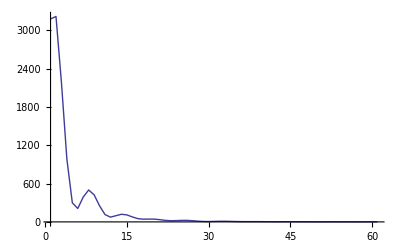

```mathematica
ListLinePlot[test⟦8⟧⟦5;;⟧,PlotRange->All]
```

```mathematica
(*hiernew*)
```